```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = Import["s_Distributions_LKJ.csv"];
```

```mathematica
mData = data[[2;;,2;;(2+16-1)]];
mData = ArrayReshape[#,{4,4}]&/@mData;
```

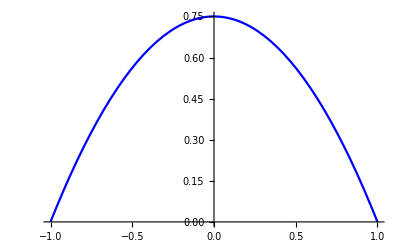

```mathematica
Plot[PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[2,2]],x],{x,-1,1},PlotStyle->Blue]
```

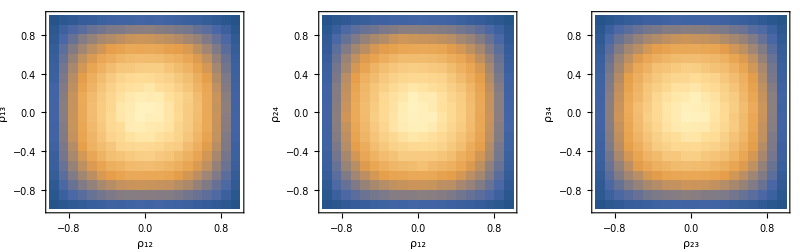

```mathematica
g1=DensityHistogram[Thread[{mData[[All,1,2]],mData[[All,1,3]]}],FrameLabel->{"ρ_12","ρ_13"},BaseStyle->Medium];
g2 = DensityHistogram[Thread[{mData[[All,1,2]],mData[[All,2,4]]}],FrameLabel->{"ρ_12","ρ_24"},BaseStyle->Medium];
g3 = DensityHistogram[Thread[{mData[[All,2,3]],mData[[All,3,4]]}],FrameLabel->{"ρ_23","ρ_34"},BaseStyle->Medium];
gFinal=Show[GraphicsRow[{g1,g2,g3}],ImageSize->800]
```

```mathematica
Export["test.pdf",gFinal]
```

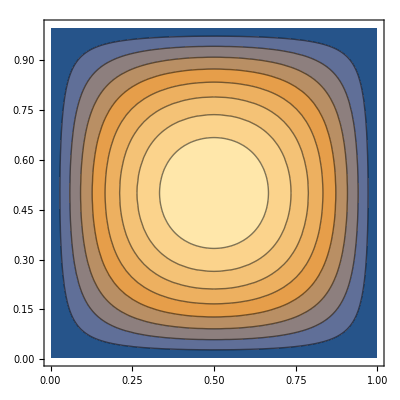

```mathematica
ContourPlot[PDF[BetaDistribution[2,2],x]*PDF[BetaDistribution[2,2],y],{x,0,1},{y,0,1}]
```